静态呈现多个切比雪夫多项式

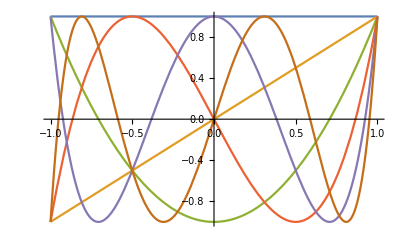

```mathematica
tableOfCheby = Table[ChebyshevT[n,x],{n,0,5}];
Plot[tableOfCheby,{x,-1,1}]
```

几个将要用到的函数

```mathematica
f0[x_]:=1/(1+25x^2);
f10[x_]:=Norm[Sin[6x]]^3 - Cos[5 Exp[x]];(*好像不解析*)
f1[x_]:=Sqrt[(Sin[6x])^6]-Cos[5Exp[x]];(*规避绝对值求导*)
f2[x_]:=1/(1+25x^2)-Sin[20x];(*正负I/5是爆破点*)
f3[x_]:=Sqrt[(Sin[5x])^6];
f4[x_]:=Sqrt[2-x];(*在2支点*)
```

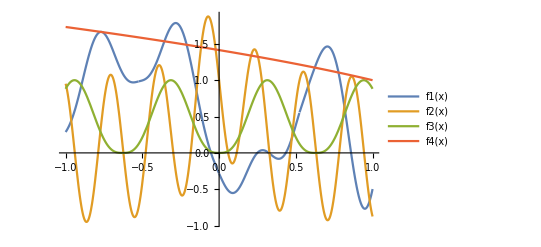

```mathematica
Plot[{f1[x],f2[x],f3[x],f4[x]},{x,-1,1},PlotLegends->LineLegend["Expressions"]](*几个函数基本的图*)
```

```mathematica
chebyPoints[a_,b_,n_]:=Module[{center = (a+b)/2,half = (b-a)/2,j},Table[center + half*Cos[j*Pi/n],{j,0,n}]];(*生成[a,b]区间的切比雪夫分点*)
```

```mathematica
valueExpandList[f_,n_]:=valueExpandList[f,n]=Module[{valuelistT1,valuelistT2,listT,i,y},listT = chebyPoints[-1,1,n];valuelistT1 = Table[f[listT[[i]]],{i,1,n+1}];valuelistT2 = Table[f[listT[[i]]],{i,n,2,-1}];
y=Flatten[{valuelistT1,valuelistT2}];y];(*把离散点周期延拓*)
fourierSum[f_,n_,j_]:=Module[{k,ylist,w = Exp[-I*Pi/n],s=0},ylist=valueExpandList[f,n];For[k=1,k≤2*n,k++,s+=(ylist[[k]]*w^((k-1)*(j-1)))];s];
chebyCoeffList[f_,n_]:=chebyCoeffList[f,n]=Module[{listA,ep,i}, ep=Table[1,{i,1,n+1}];ep[[1]]=ep[[n+1]]=2;listA=Table[1.0/(n*ep[[i]])*fourierSum[f,n,i],{i,1,n+1}];listA];(*产生切比雪夫插值的系数列表，这里如果已经算过就直接复用*)
```

```mathematica
cheby[f_,n_,x_]:=Module[{s=0,listcoeff,i},listcoeff = chebyCoeffList[f,n];For[i=1,i≤n+1,i++,s+=listcoeff[[i]]*ChebyshevT[i-1,x]];s];(*切比雪夫插值函数*)
```

```mathematica
plotShow[fun_,n_]:=Module[{list1,graph2},list1 = Plot[cheby[fun,n,x],{x,-1,1},PlotStyle->{Blue}];graph2 = Plot[fun[x],{x,-1,1},PlotStyle->{Green}];Show[graph2,list1]];
(*这里显示的是插值后的图像和原图像的对比，用来观察插值效果*)
```

```mathematica
dFun[f_,m_,x_]:=Module[{y},D[f[y],{y,m}]/.{y->x}];
showBound[f_,m_]:=Plot[Evaluate[dFun[f,m,x]],{x,-1,1},PlotStyle->{Orange}];(*这里展示各阶导数的图像*)
```

```mathematica
totalVariation[f_,m_]:=totalVariation[f,m]=Module[{listT,listT2,sum},listT=Table[dFun[f,m,x+0.01]-dFun[f,m,x],{x,-1,0.09,0.03}];listT2 = Abs[listT];sum=Apply[Plus,listT2];sum];
(*各阶导数的总变差近似值*)
coeffVariation[f_,m_,k_]:=Module[{coeffV,y},coeffV=totalVariation[f,m];y=(2*coeffV)/(Pi*((k-m-1)^(m+1)));y];(*得到切比雪夫系数估计的右式*)
errorVariation[f_,m_,n_]:=Module[{coeffV,y},coeffV=totalVariation[f,m];y=(4*coeffV)/(Pi*m*((n-m)^m));y];(*得到切比雪夫插值的最大模误差估计的右式*)
```

```mathematica
errorCheby[f_,n_]:=Module[{listT,i,listdiff,x},listT=Table[x,{x,-1,1,0.02}];listdiff=Table[Norm[f[listT[[i]]]-cheby[f,n,listT[[i]]]],{i,1,Length[listT]}];Max[listdiff//N]];(*这里显示的是切比雪夫插值的最大模误差*)
```

```mathematica
ellipseBound[f_,a_,b_]:=ellipseBound[f,a,b]=Module[{max,list,m,n,steps,thetas,i,j,result},steps=Table[x,{x,0.01,0.99,0.01}];thetas=Table[x,{x,0,2Pi,0.02}];m=Length[thetas];n=Length[steps];result=Table[Norm[f[steps[[i]]*(a*Cos[thetas[[j]]]+b*Sin[thetas[[j]]]*I)]],{i,1,n},{j,1,m}];max=Max[result]//N;max];

(*函数在指定半长轴半短轴椭圆区域内的模最大值*)
```

```mathematica
ellipseCoeff[f_,a_,b_,k_]:=Module[{bound,coeff},bound=ellipseBound[f,a,b];coeff=(2*bound)/(a+b)^(k-1);coeff];
ellipseError[f_,a_,b_,n_]:=Module[{bound,coeff},bound=ellipseBound[f,a,b];coeff=(4*bound)/(((a+b)^n)*(a+b-1));coeff];
(*这两个是Thm3涉及的两个右项*)
```

以下是结果的产生与说明

1，对于两个函数f1，f2在20,40,60个切比雪夫结点进行切比雪夫插值，作图如下

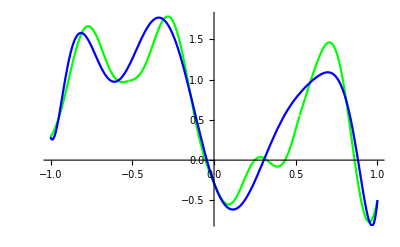

```mathematica
plotShow[f1,10]
```

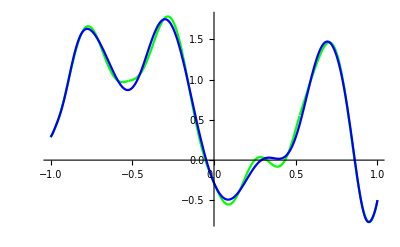
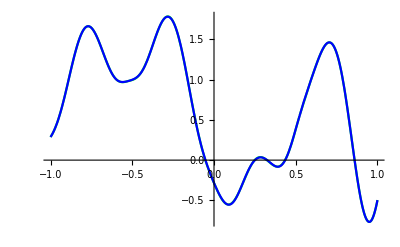
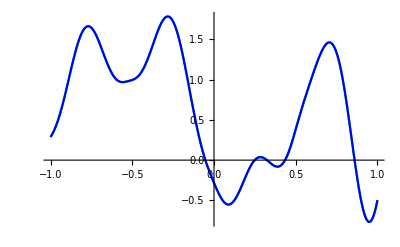
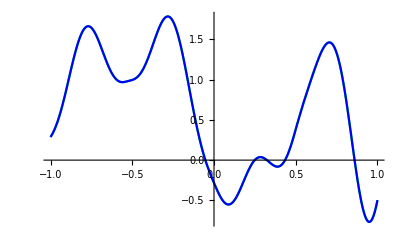
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{plotShow[f1,10],plotShow[f1,20],plotShow[f1,40],plotShow[f1,60],plotShow[f1,80]}
```

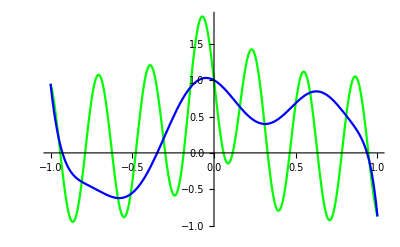
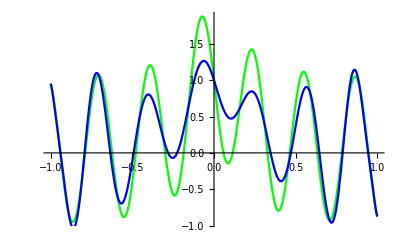
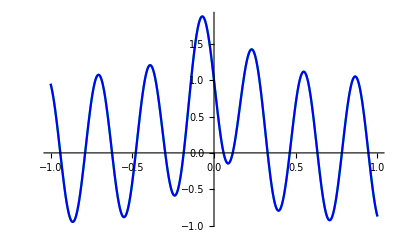
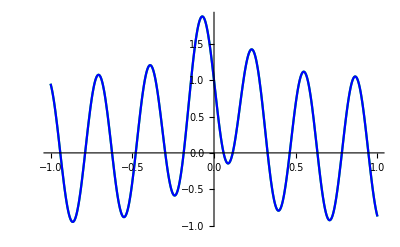
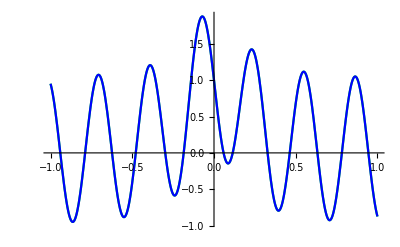

```mathematica
{plotShow[f2,10],plotShow[f2,20],plotShow[f2,40],plotShow[f2,60],plotShow[f2,80]}
```

Thm2两个函数是否满足定理需要的条件
f1的一阶导，二阶导绝对连续，三阶导不连续，但是仍然是有界变差函数，因此m可以取1,2,3

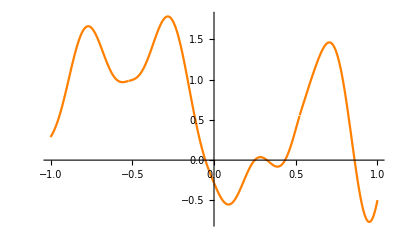
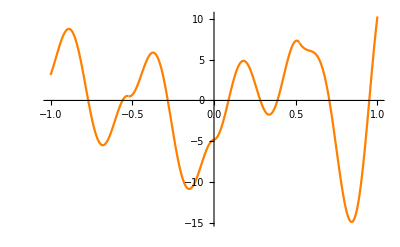
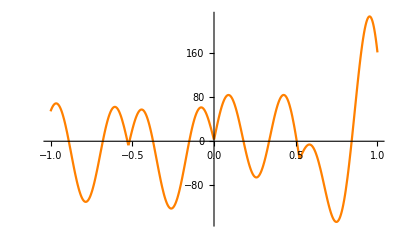
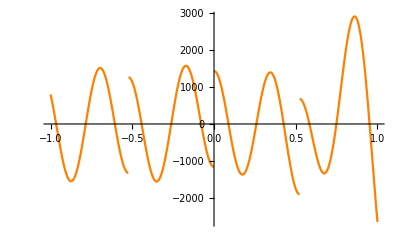

```mathematica
{showBound[f1,0],showBound[f1,1],showBound[f1,2],showBound[f1,3]}
```

f2的一阶导，二阶导......都是类似下图的函数曲线，因此各阶导数都绝对连续，m可以任取

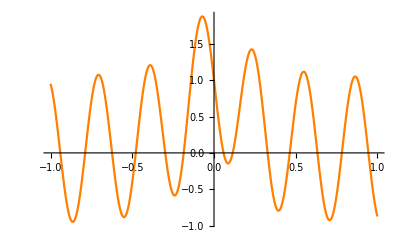
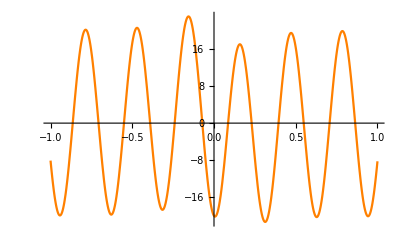
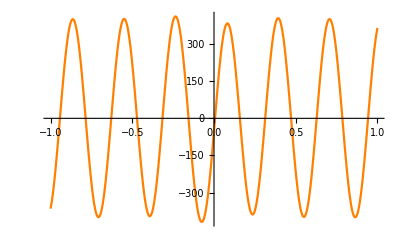
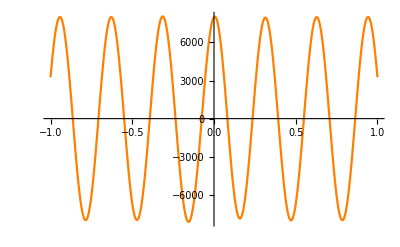

```mathematica
{showBound[f2,0],showBound[f2,1],showBound[f2,2],showBound[f2,3]}
```

Thm2的验证分为两部分，系数的控制和误差无穷范数的控制
对Thm2示例函数的验证，取m=2

```mathematica
ListPlot
```

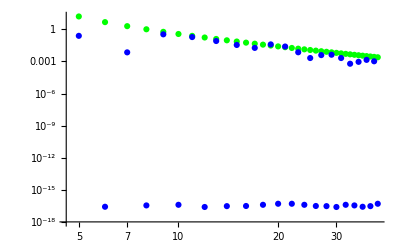

```mathematica
ListLogLogPlot[{Table[{k,coeffVariation[f3,2,k]},{k,5,40}],Table[{k,Abs[(chebyCoeffList[f3,40][[k]])]},{k,5,40}]},PlotStyle->{Green,Blue}]
```

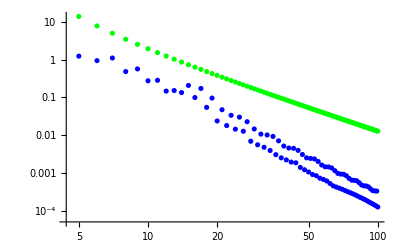

```mathematica
ListLogLogPlot[{Table[{n,errorVariation[f3,2,n]},{n,5,100,1}],Table[{n,errorCheby[f3,n]},{n,5,100,1}]},PlotStyle->{Green,Blue}]
```

对f1的验证，取m=3

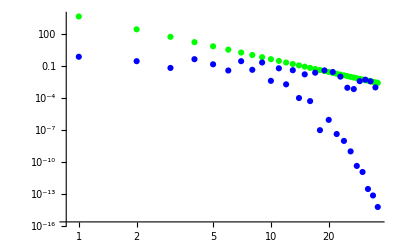

```mathematica
ListLogLogPlot[{Table[coeffVariation[f1,3,k],{k,5,40}],Table[Abs[(chebyCoeffList[f1,40][[k]])],{k,5,40}]},PlotStyle->{Green,Blue}]
```

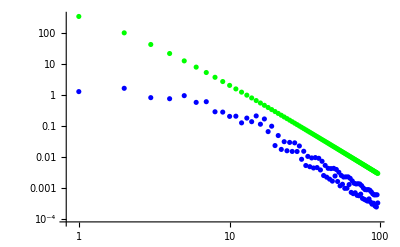

```mathematica
ListLogLogPlot[{Table[errorVariation[f1,3,n],{n,5,100,1}],Table[errorCheby[f1,n],{n,5,100,1}]},PlotStyle->{Green,Blue}]
```

对f1的验证，取m = 2

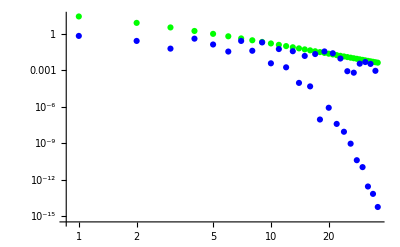

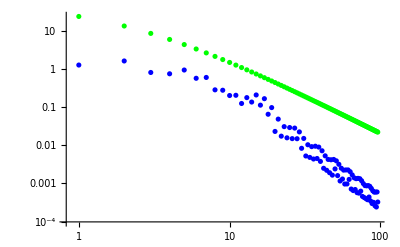

```mathematica
ListLogLogPlot[{Table[coeffVariation[f1,2,k],{k,5,40}],Table[Abs[(chebyCoeffList[f1,40][[k]])],{k,5,40}]},PlotStyle->{Green,Blue}]
ListLogLogPlot[{Table[errorVariation[f1,2,n],{n,5,100,1}],Table[errorCheby[f1,n],{n,5,100,1}]},PlotStyle->{Green,Blue}]
```

对f2的验证，取m = 3

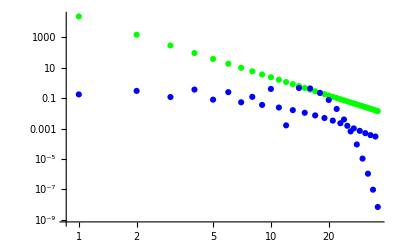

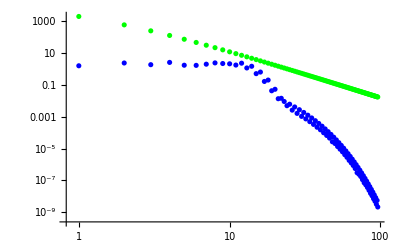

```mathematica
ListLogLogPlot[{Table[coeffVariation[f2,3,k],{k,5,40}],Table[Abs[(chebyCoeffList[f2,40][[k]])],{k,5,40}]},PlotStyle->{Green,Blue}]
ListLogLogPlot[{Table[errorVariation[f2,3,n],{n,5,100,1}],Table[errorCheby[f2,n],{n,5,100,1}]},PlotStyle->{Green,Blue}]
```

对f2的验证，取m = 4

Power::infy: 碰到无穷表达式 1/0.

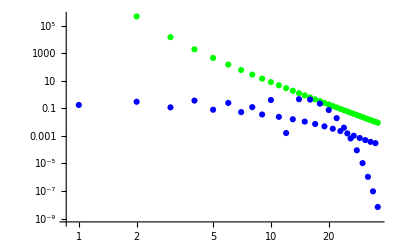

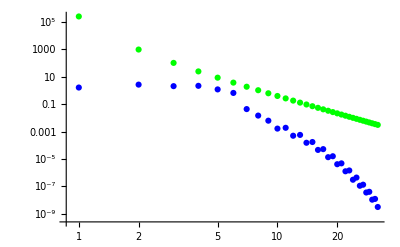

```mathematica
ListLogLogPlot[{Table[coeffVariation[f2,4,k],{k,5,40}],Table[Abs[(chebyCoeffList[f2,40][[k]])],{k,5,40}]},PlotStyle->{Green,Blue}]
ListLogLogPlot[{Table[errorVariation[f2,4,n],{n,5,100,3}],Table[errorCheby[f2,n],{n,5,100,3}]},PlotStyle->{Green,Blue}]
```

接下来Thm3的验证，首先对于示例函数进行验证，f4取长半轴2，短半轴Sqrt[3]

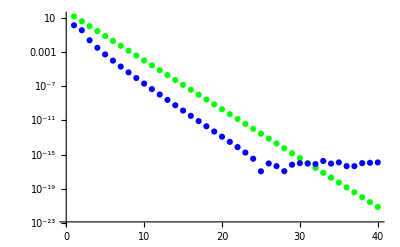

```mathematica
ListLogPlot[{Table[ellipseCoeff[f4,2,Sqrt[3],k-1],{k,1,40,1}],Table[Abs[(chebyCoeffList[f4,40][[k]])],{k,1,40,1}]},PlotStyle->{Green,Blue}]
```

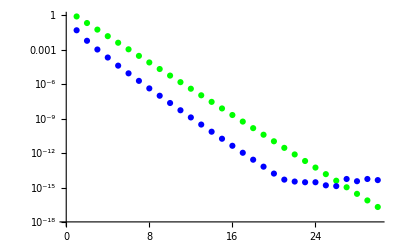

```mathematica
ListLogPlot[{Table[ellipseError[f4,2,Sqrt[3],n],{n,1,30,1}],Table[errorCheby[f4,n],{n,1,30,1}]},PlotStyle->{Green,Blue}]
```

其次是Thm3对于f1，由于在0处不解析，不适用
对于f2，由于函数在±I/5爆破，其他区域没有问题，因此选择半短轴1/5，长半轴Sqrt[1+1/25]，分别估计系数和无穷范数误差

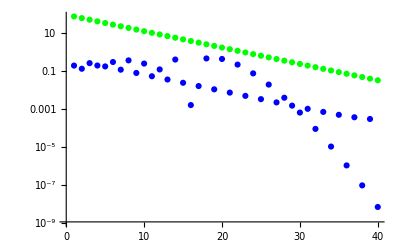

```mathematica
ListLogPlot[{Table[ellipseCoeff[f2,Sqrt[1+1/25],1/5,k],{k,1,40,1}],Table[Abs[(chebyCoeffList[f2,40][[k]])],{k,1,40,1}]},PlotStyle->{Green,Blue}]
```

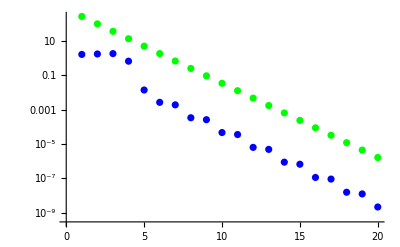

```mathematica
ListLogPlot[{Table[ellipseError[f2,Sqrt[1+1/25],1/5,n],{n,5,100,5}],Table[errorCheby[f2,n],{n,5,100,5}]},PlotStyle->{Green,Blue}]
```